## Bifurcation theory

```mathematica
blRs={AxesStyle->Black,LabelStyle->Directive[Black,12],GridLinesStyle->Directive[Black,Dotted]};
```

#### TD plane; behaviors

```mathematica
plotBF=Show[Plot[tr^2/4,{tr,-2.5,2.5},PlotRange->{-1.5,1.5},PlotStyle->{Black,Thickness[0.002]},AxesLabel->{"Tr","Det"}],Plot[{1,Abs@tr-1},{tr,-2,2},PlotStyle->{{Black,Thickness[0.002]}},Filling->{1->{2}}],blRs];
```

```mathematica
plotBF2=Show[Plot[tr^2/4,{tr,-2.5,2.5},PlotRange->{-1.5,1.5},PlotStyle->{Black,Thick},AxesLabel->{"Tr","Det"}],Plot[{1,Abs@tr-1},{tr,-2,2},PlotStyle->{{Black,Thick,Dashed}},Filling->{1->{2}}],blRs];
```

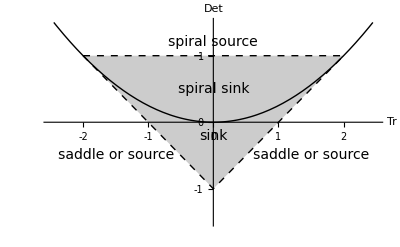

```mathematica
Show[plotBF2,Graphics[Text[Style["sink",FontSize->14,Black],{0.0,-0.2}]],Graphics[Text[Style["spiral sink",FontSize->14,Black],{0,.5}]],Graphics[Text[Style["saddle or source",FontSize->14,Black],{-1.5,-.5}]],Graphics[Text[Style["spiral source",FontSize->14,Black],{0,1.2}]],Graphics[Text[Style["saddle or source",FontSize->14,Black],{1.5,-.5}]],blRs,Ticks->{Range[-2,2],Range[-1,1]},PlotStyle->Thick]
```

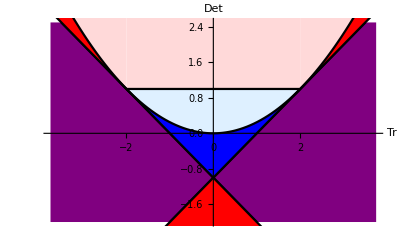

```mathematica
plotBF3=Show[Plot[{tr^2/4,tr-1,-tr-1},{tr,-3.75,3.75},PlotRange->{-2,2.5},PlotStyle->{{Black}},Filling->{2->{{3},Purple}},AxesLabel->{"Tr","Det"}],Plot[{1,tr^2/4,Abs@tr-1,-Abs@tr-1,5},{tr,-2,2},PlotStyle->{{Black}},Filling->{2->{{1},LightBlue},3->{{2},Blue},4->{Bottom,Red},1->{{5},LightRed}}],Plot[{tr^2/4,Abs@tr-1},{tr,-5,-2},PlotStyle->{{Black}},Filling->{2->{{1},Red},2->{Top,LightRed}}],Plot[{tr^2/4,Abs@tr-1},{tr,2,5},PlotStyle->{{Black}},Filling->{2->{{1},Red},2->{Top,LightRed}}],blRs]
```

```mathematica
SwatchLegend[{Red,Blue,Purple,LightRed,LightBlue},{"source","sink","saddle","spiral source","spiral sink"}]
```

```mathematica
spsink=With[{f={ Sin[x]/x^2,Cos[x]/x^2}},Show[ParametricPlot[f/.x->t,{t,8,25},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Table[{(*Hue[t/(2 Pi),1,.8],*)Arrowheads[.06],Arrow[{f,Normalize[D[f,x]]/1000+f}]}/. x->t,{t,8,25,2}]]]];
```

```mathematica
spsource=With[{f={ Sin[x]/x^2,Cos[x]/x^2}},Show[ParametricPlot[f/.x->t,{t,8,25},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Table[{(*Hue[t/(2 Pi),1,.8],*)Arrowheads[.06],Arrow[{f,Normalize[-D[f,x]]/1000+f}]}/. x->t,{t,8,25,2}]]]];
```

```mathematica
source=With[{f={{t,2t},{t,-t},{-t,-2t},{-t,t}}},Show[ParametricPlot[f,{t,.2,1},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Flatten[Table[{Arrowheads[.1],Arrow[{f,D[f,t]/10+f}⟦;;,ii⟧/.t->s]},{s,.2,1,.2},{ii,4}],1]]]];
```

```mathematica
sink=With[{f={{t,2t},{t,-t},{-t,-2t},{-t,t}}},Show[ParametricPlot[f,{t,.2,1},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Flatten[Table[{Arrowheads[.1],Arrow[{f,-D[f,t]/10+f}⟦;;,ii⟧/.t->s]},{s,.2,1,.2},{ii,4}],1]]]];
```

```mathematica
saddle=With[{f={{t,2t},{t,-t},{-t,-2t},{-t,t}}},Show[ParametricPlot[f,{t,.2,1},PlotStyle->Black,Axes->False,Epilog->{PointSize[.04],Point[{{0,0}}]}],Graphics[Flatten[Table[{Arrowheads[.1],Arrow[{f,{1,-1,1,-1}D[f,t]/10+f}⟦;;,ii⟧/.t->s]},{s,.2,1,.2},{ii,4}],1]]]];
```

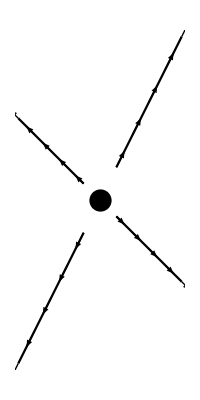
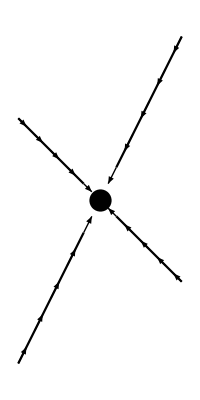
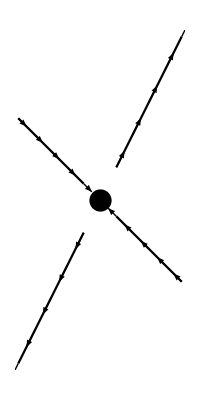
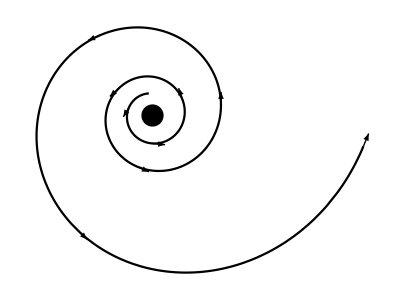
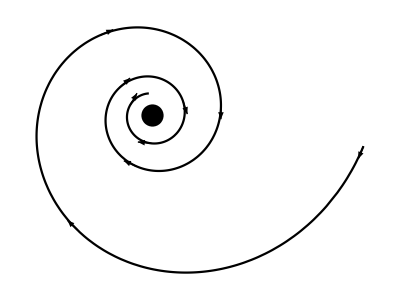

```mathematica
{source,sink,saddle,spsource,spsink}
```

## System and non-zero equilibrium

```mathematica
Clear@zpf; zpf[{T_,L_},{ω_,κ_}]=(ω L)/(1+κ T^(2/3)L);
```

```mathematica
Clear@Tf; Tf[{T_,z_},{μ_}]=T Exp[μ-z];
Clear@Lf; Lf[{T_,L_},{λ_,ρ_}]=(1-λ) L+ρ T;
```

```mathematica
Clear@SysF;SysF[{T_,L_},{ω_,κ_,μ_,ρ_,λ_}]:={Tf[{T,zpf[{T,L},{ω,κ}]},{μ}],
Lf[{T,L},{λ,ρ}]}
```

```mathematica
var={T,L};
par={ω,κ,μ,ρ,λ};
```

```mathematica
(*equilibria*)
κeqR=κ->(-λ μ+T ρ ω)/(T^(5/3) μ ρ);
λeqR=λ->-(T ρ (T^(2/3) κ μ-ω))/μ;
ωeqR=ω->(μ (λ+T^(5/3) κ ρ))/(T ρ);
LeqR=L->(T ρ/λ);

(*bifurcation*)
TbfR=T->(5 λ μ)/(2 ρ ω);
κbfR=κ->(3 (2/5)^(2/3) ω)/(5 μ ((λ μ)/(ρ ω))^(2/3));
λbfR=λ->(6 √(3/5) ρ ω^(5/2))/(25 κ^(3/2) μ^(5/2));
ωbfR=ω->(5  κ^(3/5) λ^(2/5) μ)/(2^(2/5)3^(3/5) ρ^(2/5));

(*jacobian*)
J=Simplify[D[SysF[var,par],{var}]/.LeqR];
```

## Equilibrium Analysis

### Bifurcation diagrams

#### For κ

```mathematica
par1={0.135,0,.217,.5,0.045};

J1=J/.κ->κp/.Thread[par->par1]/.κp->κ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
κR1=κ/.κeqR/.Thread[par->par1];
```

```mathematica
{κbp,Lbp,Tbp}={κ/.κbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
Tκ0=T/.Solve[(κ/.κeqR/.Thread[par->par1])==0,T]⟦1⟧;
```

```mathematica
tkR=Ticks->{{{0,0},{κbp/.Thread[par->par1],SuperStar[κ]}},Thread[{{(μ λ)/(ω ρ),(5μ λ)/(2ω ρ)}/.Thread[par->par1],{(μ λ)/(ω ρ),(5μ λ)/(2ω ρ)}}]};
glR=GridLines->{{0,κbp},{2/5 T,T}/.TbfR/.Thread[par->par1]};
```

```mathematica
plt1=Show[ParametricPlot[{κR1,T},{T,Tκ0,Tbp},GridLinesStyle->Directive[{Black,Dashed}],Evaluate@{PlotStyle->Black,PlotRange->{{0,1},{0,1.3}},AxesLabel->{"κ","T"},glR,blRs},GridLinesStyle->Directive[Black,Dashing[{0,Small}],Thickness[20]],AspectRatio->1/GoldenRatio],ParametricPlot[{κR1,T},{T,Tbp,500},PlotStyle->{Dashed,Black}],Graphics[{EdgeForm[Thick],Black,Disk[{κbp,T/.TbfR}/.Thread[par->par1],{.015,.03}],White,Disk[{0,Tκ0}/.Thread[par->par1],{.015,.03}]}]];
```

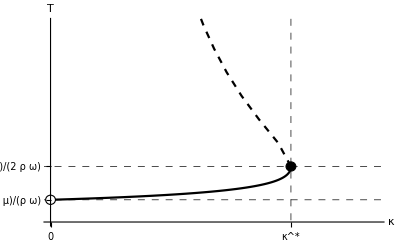

```mathematica
Show[plt1,tkR]
```

```mathematica
L1=NSolve[(((((ω L)/μ-1)/(κ L))^(3/2)/.κ->0.8κbp)==(L λ)/ρ)/.Thread[par->par1],L];
```

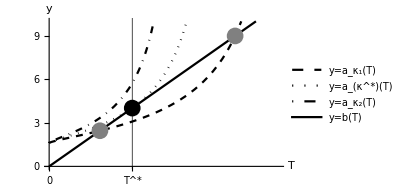

```mathematica
Plot[Evaluate[Append[(μ/(ω-μ κ T^(2/3)))/.κ->κbp{0.8,1,1.2},(T ρ)/λ]/.Thread[par->par1]],{T,0,1},PlotRange->{0,10},Ticks->{{0,{(L λ)/ρ/.L->Lbp/.Thread[par->par1],SuperStar[T]}},None},AxesLabel->{"T","y"},GridLines->{{(L λ)/ρ/.L->Lbp/.Thread[par->par1]},None},GridLinesStyle->Directive[{Black}],Epilog->{PointSize[0.04],Gray,Point[{(L λ)/ρ,L}/.Thread[par->par1]/.L1],PointSize[0.04],Black,Point[{(L λ)/ρ,L}/.L->Lbp/.Thread[par->par1]]},PlotStyle->{{Black,Dashed},{Black, Dotted},{Black,DotDashed},Black},LabelStyle->{{Black,Thick,12}},PlotLegends->Placed[{"y=a_κ_1(T)","y=a_(κ^*)(T)","y=a_κ_2(T)","y=b(T)"},{.82,.3}],ImageSize->300]
```

#### For ρ/λ (ρ is fixed)

```mathematica
par1={0.05,(*κ1 of weak immune*)0.005840029739549371,.217,ρ1=.1,0.335};
```

```mathematica
J1=J/.λ->λp/.Thread[par->par1]/.λp->λ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
λR1=λ/.λeqR/.Thread[par->par1];
```

```mathematica
{λbp,Lbp,Tbp}={λ/.λbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
```

```mathematica
Tbp=T/.Solve[D[1/λR1,T]==0,T]⟦1⟧;
Trg=Sort[T/.Solve[Simplify[1/D[1/λR1,T]]==0,T]/.(0.->.1)];
```

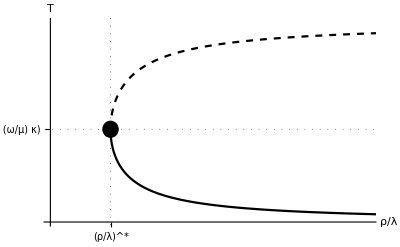

```mathematica
tkR=Ticks->{{{ρ1/λbp,"(ρ/λ)^*"}},{{Tbp,"5/(2 (ω/μ) κ)"}}};
glR=GridLines->{{ρ1/λbp},{Tbp}};
marker=Graphics[{EdgeForm[Thick],Black,Disk[{ρ1/λbp,Tbp},{.012,10}]}];
Show[ParametricPlot[{ρ1/λR1,T},{T,Trg⟦1⟧,Tbp},Evaluate@{PlotStyle->Black,PlotRange->{{0,.5},{0,Trg⟦2⟧}},AxesLabel->{"ρ/λ","T"},blRs,tkR,glR},AspectRatio->1/GoldenRatio],ParametricPlot[{ρ1/λR1,T},{T,Tbp,5Trg⟦2⟧},PlotStyle->{Dashed,Black}],marker]
```

#### For μ/ω (μ is fixed)

```mathematica
par1={0.05,(*κ1 of weak immune*)0.005840029739549371,μ1=.217,.1,0.335};
```

```mathematica
J1=J/.ω->ωp/.Thread[par->par1]/.ωp->ω;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
ωR1=ω/.ωeqR/.Thread[par->par1];
```

```mathematica
{ωbp,Lbp,Tbp}={ω/.ωbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
```

```mathematica
Tbp=T/.Solve[D[1/ωR1,T]==0,T]⟦1⟧;tkR=Ticks->{{{μ1/ωbp,"(μ/ω)^*"}},{{Tbp,(*fix this*)"(3/(2  κ (ρ/λ)))^(3/5)"}}};
```

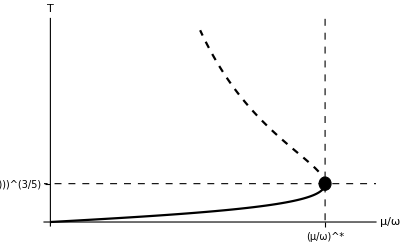

```mathematica
glR=GridLines->{{μ1/ωbp},{Tbp}};
marker=Graphics[{EdgeForm[Thick],Black,Disk[{μ1/ωbp,Tbp},{.15,10}]}];
Show[ParametricPlot[{μ1/ωR1,T},{T,0,Tbp},Evaluate@tkR,GridLinesStyle->Directive[Thickness[.002],Black,Dashed],PlotStyle-> Black,PlotRange->{{0,8(*.5*)},{0,300(*5Tbp⟦1⟧*)}},AxesLabel->{"μ/ω","T"},Evaluate@blRs,Evaluate@glR,AspectRatio->1/GoldenRatio],ParametricPlot[{μ1/ωR1,T},{T,Tbp,5Tbp},PlotStyle->{Dashed,Black}],marker]
```

### Weak immune system

```mathematica
par1={0.05,0,μ1=.217,ρ1=.1,0.335};
```

#### Bifurcation in terms of κ

```mathematica
J1=J/.κ->κp/.Thread[par->par1]/.κp->κ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
κR1=κ/.κeqR/.Thread[par->par1];

{κbp,Lbp,Tbp}={κ/.κbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
Tκ0=T/.Solve[(κ/.κeqR/.Thread[par->par1])==0,T]⟦1⟧;

TbpAllR=FindRoot[Simplify[#/.κeqR/.Thread[par->par1]]==0,{T,Mean@{Tκ0,Tbp}}]&/@{(*det1-1,*)tr1^2-4det1,det1-tr1+1}
κbpAll=κ/.κeqR/.TbpAllR/.Thread[par->par1]

TDbp=MapThread[{tr1,det1}/.{T->#1,κ->#2}&,{TbpAllR⟦;;,1,2⟧,κbpAll}];

κbpE=κbpAll⟦1⟧;
TbpE=T/.FindRoot[κR1==κbpE,{T,#}]&/@{Tκ0,2Tbp};
TDbpE=Thread[{tr1,det1}/.{T->TbpE,κ->κbpE}];

(*Case 1*)κ1=.5κbpAll⟦1⟧;
T1=T/.FindRoot[κR1==κ1,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ1}];

(*Case 2*)κ2=Mean[κbpAll];
T2=T/.FindRoot[κR1==κ2,{T,#}]&/@{Tκ0,2Tbp};
TD2=Thread[{tr1,det1}/.{T->T2,κ->κ2}];
```

{{T→26.4167},{T→36.3475}}

{0.0116801,0.0125993}

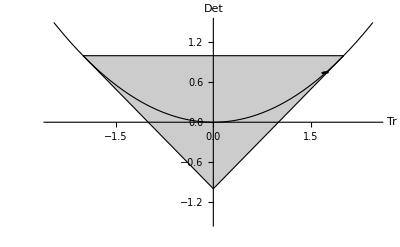

```mathematica
plotTD=Show[ParametricPlot[{tr1,det1}/.κeqR/.Thread[par->par1],{T,#⟦1⟧,#⟦2⟧},PlotStyle->#⟦3⟧]&/@{{Tκ0,2T1⟦2⟧,{Black,Dashed}},{Tκ0,Tbp,Black}}];

pr1={{1.65,1.82},{0.73,0.77}};Show[plotBF,plotTD,Graphics[{EdgeForm[Thin],Opacity[0],Rectangle@@({.95,1.05}Thread@pr1)}]]
```

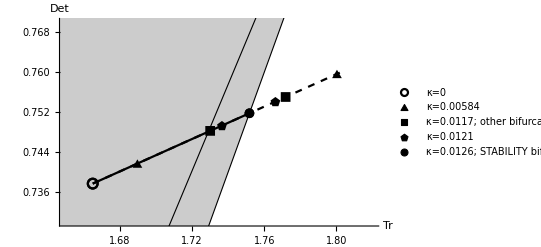

```mathematica
Show[plotBF,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE,TD2,{TDbp⟦2⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 10},{Graphics[RegularPolygon[5]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ=0.00584","κ=0.0117; other bifurcation","κ=0.0121","κ=0.0126; STABILITY bifurcation (saddle-node)"}],PlotRange->pr1]
```

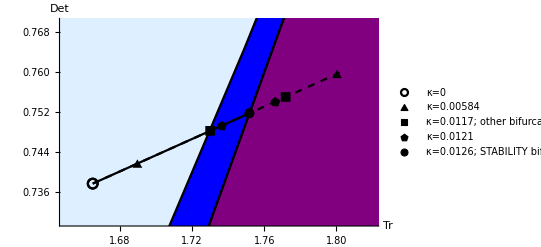

```mathematica
Show[plotBF3,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE,TD2,{TDbp⟦2⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 10},{Graphics[RegularPolygon[5]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ=0.00584","κ=0.0117; other bifurcation","κ=0.0121","κ=0.0126; STABILITY bifurcation (saddle-node)"}],PlotRange->pr1]
```

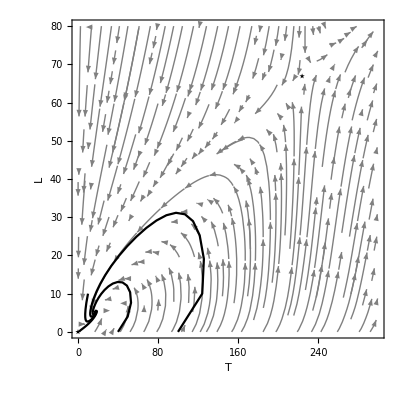
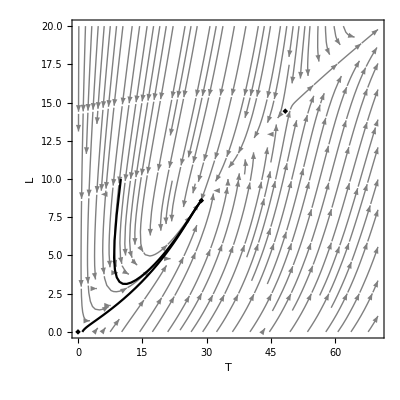
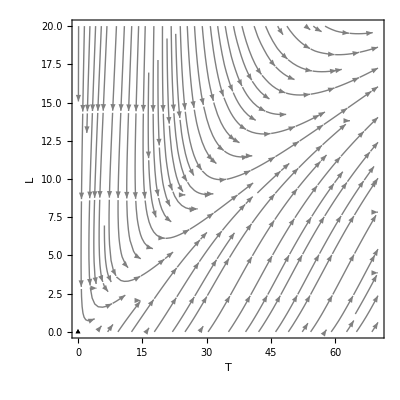

```mathematica
stream=Table[Block[{k={κ1,κ2,2κ2}⟦ii⟧},Show[StreamPlot[SysF[{T,L},par/.κ->k/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,{300,70,70}⟦ii⟧},{L,0,{80,20,20}⟦ii⟧},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[k,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->k/.Thread[par->par1]/.T->Append[{T1,T2,{}}⟦ii⟧,0]],PlotMarkers->{★,◆,▲}⟦ii⟧,PlotStyle->Black]]],{ii,3}];

n=500;res=Table[Block[{parB=par/.κ->{κ1,κ2,2κ2}⟦jj⟧/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{jj,3},{ini,{{1,0},{10,10},{40,0},{100,0},{200,0}}}];

TLplot=ListLinePlot[#,PlotRange->All,PlotStyle->Black,Frame->True,FrameLabel->{"T","L"},FrameStyle->Black]&/@res;

MapThread[Show,{stream,TLplot}]
```

#### Bifurcation in terms of ρ/λ (ρ is fixed)

```mathematica
κlist={0.005840029739549371,0.012139661468677416,0.02427932293735483};
```

```mathematica
J1=Table[J/.κ->k/.λ->λp/.Thread[par->par1]/.λp->λ,{k,κlist}];
det1=Simplify@Det/@J1;
tr1=Simplify@Tr/@J1;
λR1=Table[λ/.λeqR/.κ->k/.λ->λp/.Thread[par->par1]/.λp->λ,{k,κlist}];
```

```mathematica
Tbp=T/.Solve[D[1/#,T]==0,T]⟦1⟧&/@λR1;
Trg=(Sort[T/.Solve[Simplify[1/D[1/#,T]]==0,T]]&/@λR1)/.(0.->.1);
T0=Table[T/.Solve[(κ/.κeqR/.λ->0/.Thread[par->par1])==κlist⟦ii⟧,T]⟦1⟧,{ii,3}];
```

```mathematica
plotTD=Table[Show[ParametricPlot[{tr1⟦ii⟧,det1⟦ii⟧}/.λ->λR1⟦ii⟧/.Thread[par->par1],{T,Trg⟦ii,1⟧,Tbp⟦ii⟧},PlotStyle->#⟦3⟧],ParametricPlot[{tr1⟦ii⟧,det1⟦ii⟧}/.λ->λR1⟦ii⟧/.Thread[par->par1],{T,Tbp⟦ii⟧,Trg⟦ii,2⟧},PlotStyle->{Black,Dashed}],Graphics[{EdgeForm[Thick],Black,Disk[{tr1⟦ii⟧,det1⟦ii⟧}/.λ->λR1⟦ii⟧/.Thread[par->par1]/.T->Tbp⟦ii⟧,{.015,.025}]}]]&/@{{T0⟦1⟧,100,{Black,Dashed}},{T0⟦1⟧,Tbp,Black}},{ii,3}];
```

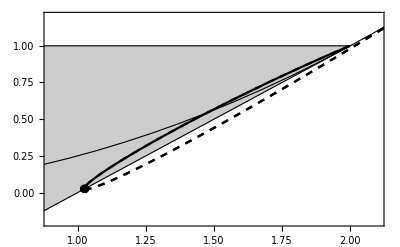
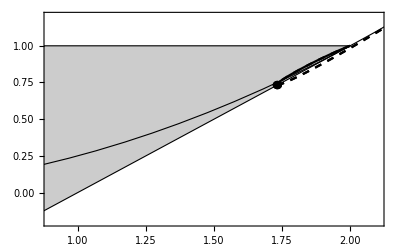
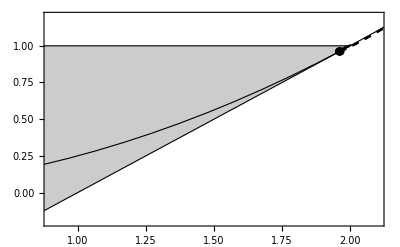

```mathematica
Show[plotBF,#,PlotRange->{1.5+.6{-1,1},.5+.7{-1,1}},Frame->True,AxesLabel->None]&/@plotTD
```

#### Bifurcation in terms of μ/ω (μ is fixed)

```mathematica
κlist={0.005840029739549371,0.012139661468677416,0.02427932293735483};
```

```mathematica
J1=Table[J/.κ->k/.ω->ωp/.Thread[par->par1]/.ωp->ω,{k,κlist}];
det1=Simplify@Det/@J1;
tr1=Simplify@Tr/@J1;
ωR1=Table[ω/.ωeqR/.κ->k/.ω->ωp/.Thread[par->par1]/.ωp->ω,{k,κlist}];
```

```mathematica
Tbp=T/.Solve[D[1/#,T]==0,T]⟦1⟧&/@ωR1;
(*Trg=(Sort[T/.Solve[Simplify[1/D[1/#,T]]==0,T]]&/@λR1)/.(0.->.1);*)
T0=Table[T/.Solve[(κ/.κeqR/.λ->0/.Thread[par->par1])==κlist⟦ii⟧,T]⟦1⟧,{ii,3}];
```

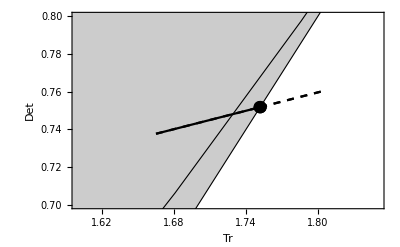
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotTD=Table[Show[ParametricPlot[{tr1⟦ii⟧,det1⟦ii⟧}/.ω->ωR1⟦ii⟧/.Thread[par->par1],{T,(*0*)Tbp⟦ii⟧/1000,Tbp⟦ii⟧},PlotStyle->#⟦3⟧],ParametricPlot[{tr1⟦ii⟧,det1⟦ii⟧}/.ω->ωR1⟦ii⟧/.Thread[par->par1],{T,Tbp⟦ii⟧,5Tbp⟦ii⟧},PlotStyle->{Black,Dashed}],Graphics[{EdgeForm[Thick],Black,Disk[{tr1⟦ii⟧,det1⟦ii⟧}/.ω->ωR1⟦ii⟧/.Thread[par->par1]/.T->Tbp⟦ii⟧,{.005,.003}]}]]&/@{{T0⟦1⟧,100,{Black,Dashed}},{T0⟦1⟧,Tbp,Black}},{ii,3}];
Show[plotBF,#,PlotRange->{{1.6,1.85},0.75+.05{-1,1}},Frame->True]&/@plotTD
```

### Strong immune system

```mathematica
par1={.135,0,.217,.5,.045};
```

#### Bifurcation in terms of κ

```mathematica
J1=J/.κ->κp/.Thread[par->par1]/.κp->κ;
det1=Simplify@Det[J1];
tr1=Simplify@Tr[J1];
κR1=κ/.κeqR/.Thread[par->par1];

{κbp,Lbp,Tbp}={κ/.κbfR,L/.LeqR,T}/.TbfR/.Thread[par->par1];
Tκ0=T/.Solve[(κ/.κeqR/.Thread[par->par1])==0,T]⟦1⟧;
```

```mathematica
TbpAllR=FindRoot[Simplify[#/.κp->κ/.κeqR/.Thread[par->par1]]==0,{T,Mean@{Tκ0,Tbp}}]&/@{det1-1,tr1^2-4det1,det1-tr1+1};
κbpAll=κ/.κeqR/.TbpAllR/.Thread[par->par1];
TDbp=MapThread[{tr1,det1}/.{T->#1,κ->#2}&,{TbpAllR⟦;;,1,2⟧,κbpAll}];
```

```mathematica
(*early BF*)κbpE1=κbpAll⟦1⟧;
TbpE1=T/.FindRoot[κR1==κbpE1,{T,#}]&/@{Tκ0,2Tbp};
TDbpE1=Thread[{tr1,det1}/.{T->TbpE1,κ->κbpE1}];

κbpE2=κbpAll⟦2⟧;
TbpE2=T/.FindRoot[κR1==κbpE2,{T,#}]&/@{Tκ0,2Tbp};
TDbpE2=Thread[{tr1,det1}/.{T->TbpE2,κ->κbpE2}];
```

```mathematica
(*Case 1*)κ1=.9κbpAll⟦1⟧;
T1=T/.FindRoot[κR1==κ1,{T,#}]&/@{Tκ0,2Tbp};
TD1=Thread[{tr1,det1}/.{T->T1,κ->κ1}];
```

```mathematica
(*Case 2*)κ2=Mean[κbpAll⟦;;2⟧];
T2=T/.FindRoot[κR1==κ2,{T,#}]&/@{Tκ0,2Tbp};
TD2=Thread[{tr1,det1}/.{T->T2,κ->κ2}];
```

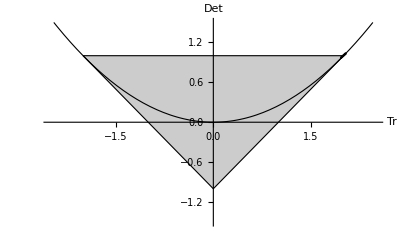

```mathematica
plotTD=Show[ParametricPlot[{tr1,det1}/.κeqR/.Thread[par->par1],{T,#⟦1⟧,#⟦2⟧},PlotStyle->#⟦3⟧]&/@{{Tκ0,2T1⟦2⟧,{Black,Dashed}},{Tκ0,Tbp,Black}}];

pr1={{1.944,2.1},{.95,1.09}};Show[plotBF,plotTD,Graphics[{EdgeForm[Thin],Opacity[0],Rectangle@@({.95,1.05}Thread@pr1)}]]
```

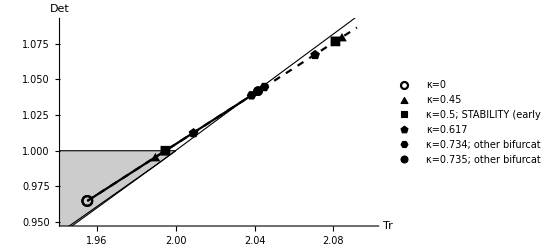

```mathematica
Show[plotBF,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE1,TD2,TDbpE2,{TDbp⟦3⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 10},{Graphics[RegularPolygon[5]],10},{Graphics[RegularPolygon[6]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ=0.45","κ=0.5; STABILITY (early) bifurcation","κ=0.617","κ=0.734; other bifurcation","κ=0.735; other bifurcation (saddle-node)"}],PlotRange->pr1]
```

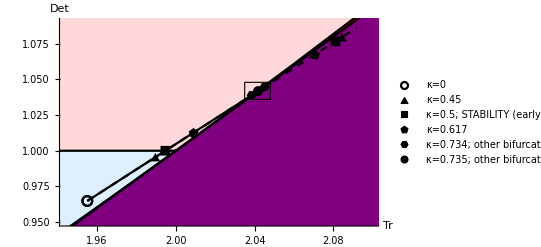

```mathematica
Show[Show[plotBF3,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE1,TD2,TDbpE2,{TDbp⟦3⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 10},{Graphics[RegularPolygon[5]],10},{Graphics[RegularPolygon[6]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ=0.45","κ=0.5; STABILITY (early) bifurcation","κ=0.617","κ=0.734; other bifurcation","κ=0.735; other bifurcation (saddle-node)"}],PlotRange->pr1],Graphics[{EdgeForm[Thick],Opacity[0],Rectangle@@(Thread@{{2.035,2.048},{1.036,1.048}})}]]
```

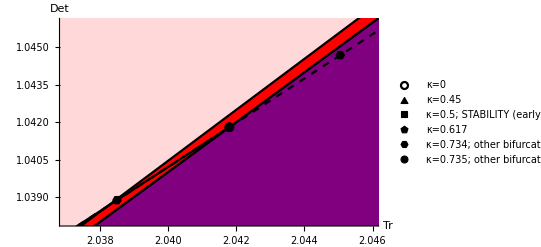

```mathematica
Show[plotBF3,plotTD,ListPlot[{{{tr1,det1}/.{T->Tκ0,κ->0}},TD1,TDbpE1,TD2,TDbpE2,{TDbp⟦3⟧}},PlotStyle->{{Black}},PlotMarkers->{{Graphics[Circle[]], 10},{Graphics[RegularPolygon[3]], 10},{Graphics[Rectangle[]], 10},{Graphics[RegularPolygon[5]],10},{Graphics[RegularPolygon[6]],10},{Graphics[Disk[]], 10}},PlotLegends->{"κ=0","κ=0.45","κ=0.5; STABILITY (early) bifurcation","κ=0.617","κ=0.734; other bifurcation","κ=0.735; other bifurcation (saddle-node)"}],PlotRange->{{2.037,2.046},{1.038,1.046}}]
```

```mathematica
stream=Table[Block[{k={κ1,κ2,2κ2}⟦ii⟧},Show[StreamPlot[SysF[{T,L},par/.κ->k/.Thread[par->par1]]⟦;;2⟧-{T,L},{T,0,{2,1,1}⟦ii⟧},{L,0,{20,10,10}⟦ii⟧},StreamPoints->Fine,StreamStyle->Gray,StreamColorFunction->None,FrameLabel->{"T","L","κ="<>ToString[NumberForm[k,3]]},FrameStyle->Black,LabelStyle->Large],ListPlot[Thread[{T,L}/.LeqR/.κ->k/.Thread[par->par1]/.T->Append[{T1,T2,{}}⟦ii⟧,0]],PlotMarkers->{★,◆,▲}⟦ii⟧,PlotStyle->Black]]],{ii,3}];
```

```mathematica
n=500;res=Table[Block[{parB=par/.κ->{κ1,κ2,2κ2}⟦jj⟧/.Thread[par->par1]},NestList[SysF[#,parB]&,ini,n]]⟦;;,;;2⟧,{jj,3},{ini,{{1.3,10},{.2,2},{.7,7}}}];
```

```mathematica
TimeSeriesplot=Table[Show@@(ListLinePlot[Thread@#,PlotRange->All,PlotLegends->Placed[{"T","L"(*,"A","DM"*)},{.2,.8}],Frame->True,FrameLabel->{"time"},FrameStyle->Black]&/@r),{r,res}];
TLplot=ListLinePlot[#,PlotRange->All,PlotStyle->Black(*,Epilog->{PointSize[Medium],Point[{#⟦1,;;2⟧}]}*),Frame->True,FrameLabel->{"T","L"},FrameStyle->Black]&/@res;(*TableForm[{TimeSeriesplot,TLplot},TableHeadings->{None,("κ="<>ToString@#)&/@{κ1,κ2,2κ2}}]*)
```

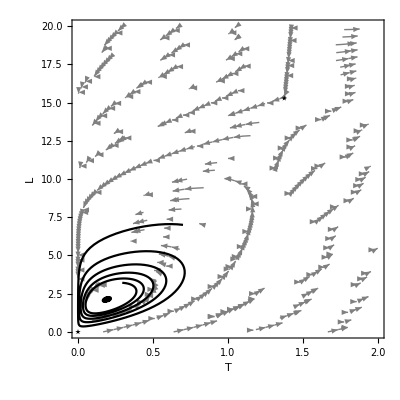
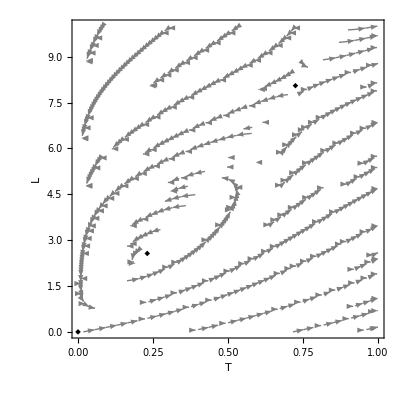
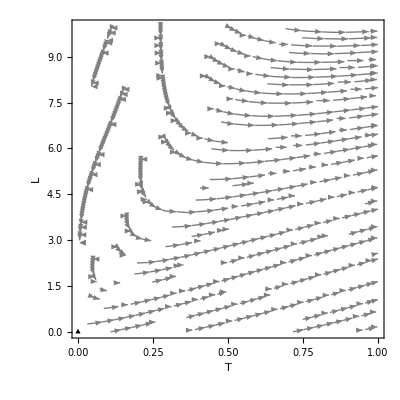

```mathematica
MapThread[Show,{stream,TLplot}]
```